## Analysis of Antigen output

## Basic parameters

```mathematica
demeCount=3;
```

```mathematica
demes={"north","tropics","south"};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/antigen

```mathematica
SetDirectory["example/"]
```

/Users/bedfordt/Documents/current-projects/antigen/example

```mathematica
spatialColors={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

```mathematica
spatialColors=Map[Lighter[#,0.1]&,spatialColors]
```

{RGBColor[0.7885,0.7552,0.3466],RGBColor[0.3916,0.6481,0.7372],RGBColor[0.8713,0.2179,0.2188]}

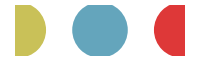

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,spatialColors]},PlotRange->All,AspectRatio->0.3,ImageSize->200]
```

```mathematica
spatialColorRules=MapIndexed[#2[[1]]-1->#1&,spatialColors];
```

```mathematica
k=11;
```

```mathematica
mod=8;
```

```mathematica
clusterColors=Table[Lighter[ColorData["Rainbow"][FractionalPart[i-0.001]],0.1],{i,1/k,mod,mod/k}];
```

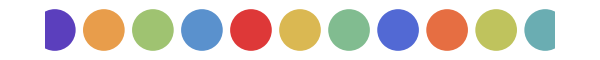

```mathematica
Graphics[{PointSize[0.05],MapIndexed[{#1,Point[{#2[[1]],0}]}&,clusterColors]},PlotRange->All,AspectRatio->0.1,ImageSize->600]
```

```mathematica
narrowWidth=255;
```

```mathematica
extraNarrowWidth=215;
```

```mathematica
padding={{35,5},{20,15}};
```

```mathematica
fullPadding={{37,2},{29,5}};
```

```mathematica
partialPadding={{15,2},{13,2}};
```

```mathematica
imageSize=500;
```

## Loess fit

```mathematica
LoessFit[(x_)?VectorQ,data_,α_:0.75,λ_:1]:=Table[LoessFit[x[[i]],data,α,λ],{i,Length[x]}]
```

```mathematica
LoessFit[(x_)?NumberQ,data_,α_:0.75,λ_:1]:=WLSFit[data,LoessWts[x,data,α],λ,x];
```

```mathematica
WLSFit[data_,wts_,ldegree_:1,x_]:=Fit[Transpose[(wts*#1&)/@Join[{Table[1,{Length[data]}]},Transpose[data]]],Join[{u},Table[v^i,{i,ldegree}]],{u,v}]/.{u->1,v->x}
```

```mathematica
LoessWts[x_,data_,α_]:=Tricube[(x-First[Transpose[data]])/LoessDistance[x,data,α]]
```

```mathematica
Tricube=Compile[{{x,_Real,1}},If[Abs[#]<1,(1-Abs[#]^3)^3,0]&/@x];
```

```mathematica
LoessDistance[x_,data_,α_]:=Module[{A=Max[1,α],X=First[Transpose[data]],q},q=Min[Length[X],Ceiling[α*Length[X]]];A*Sort[Abs[X-x]][[q]]]
```

## Options

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize];
```

```mathematica
SetOptions[ContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->imageSize];
```

```mathematica
SetOptions[DiscretePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->imageSize,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->imageSize,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->imageSize,PlotRange->{0,All}];
```

## Timeseries

### Data import

Assuming weekly output

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,data[[1]]]
```

{date→1,div→2,tmrca→3,netau→4,totalN→5,totalS→6,totalI→7,totalR→8,totalCases→9,northDiv→10,northTmrca→11,northNetau→12,northN→13,northS→14,northI→15,northR→16,northCases→17,tropicsDiv→18,tropicsTmrca→19,tropicsNetau→20,tropicsN→21,tropicsS→22,tropicsI→23,tropicsR→24,tropicsCases→25,southDiv→26,southTmrca→27,southNetau→28,southN→29,southS→30,southI→31,southR→32,southCases→33}

```mathematica
data=Drop[data,1];
```

```mathematica
date="date"/.headerRules
```

1

```mathematica
startTime=data[[1,date]]
```

0.0822

```mathematica
endTime=data[[-1,date]]
```

19.9726

```mathematica
stepTime=data[[2,date]]-data[[1,date]]
```

0.0822

```mathematica
popSize=data[[1,"totalN"/.headerRules]]
```

7500000

```mathematica
demePopSize=popSize/demeCount
```

2500000

### Prevalence

```mathematica
index="totalI"/.headerRules
```

7

```mathematica
N[Mean[data[[All,index]]]]
```

11945.4

```mathematica
N[HarmonicMean[data[[All,index]]]]
```

748.83

```mathematica
prev=Transpose[{data[[All,date]],(data[[All,index]]*100000)/popSize}];
```

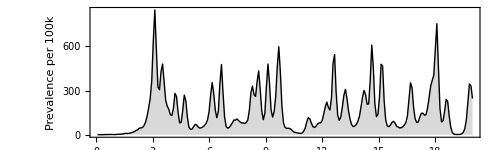

```mathematica
fig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"","Prevalence per 100k"},ImagePadding->{{40,10},{15,5}}]
```

```mathematica
Export["prevalence.pdf",fig,"PDF"]
```

prevalence.pdf

### Incidence

```mathematica
index="totalCases"/.headerRules
```

9

```mathematica
inc=Transpose[{data[[All,date]],(data[[All,index]]*100000)/popSize}];
```

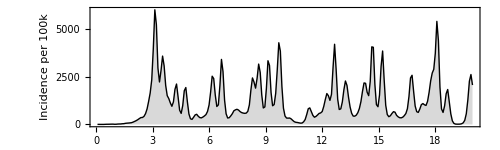

```mathematica
fig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"Year","Incidence per 100k"}]
```

```mathematica
Export["incidence.pdf",fig,"PDF"]
```

incidence.pdf

Mean incidence per year

```mathematica
meaninc=N[(Total[data[[All,index]]]/endTime)/popSize]
```

0.145014

Flu incidence for H3N2 is around 8% per year.

### Deme-specific yearly incidence

```mathematica
indices=Map[#<>"Cases"&,demes]/.headerRules
```

{17,25,33}

```mathematica
incList=Table[data[[All,i]],{i,indices}];
```

```mathematica
meanIncList=Map[Total[#]&,incList]/((endTime-startTime)*(popSize/demeCount));
```

```mathematica
TableForm[Round[meanIncList,0.001],TableHeadings->{demes}]
```

north | 0.145
tropics | 0.145
south | 0.147

### Deme-specific prevalence

```mathematica
indices=Map[#<>"I"&,demes]/.headerRules
```

{15,23,31}

```mathematica
prevList=N[Table[Transpose[{data[[All,date]],data[[All,i]]*100000/demePopSize}],{i,indices}]];
```

```mathematica
max=Max[Map[Max,prevList[[All,All,2]]]]
```

1967.32

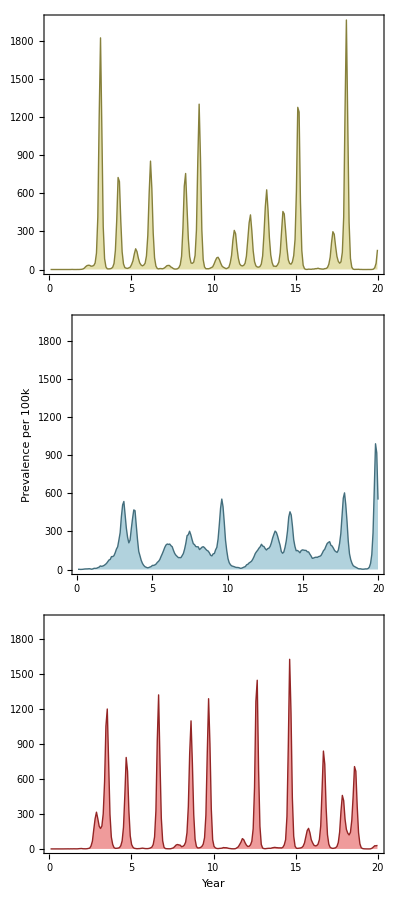

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Prevalence per 100k",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["prevalenceSpatial.pdf",fig,"PDF"]
```

prevalenceSpatial.pdf

### Absolute prevalence

```mathematica
indices=Map[#<>"I"&,demes]/.headerRules
```

{15,23,31}

```mathematica
prevList=N[Table[Transpose[{data[[All,date]],data[[All,i]]}],{i,indices}]];
```

```mathematica
max=Max[Map[Max,prevList[[All,All,2]]]]
```

49183.

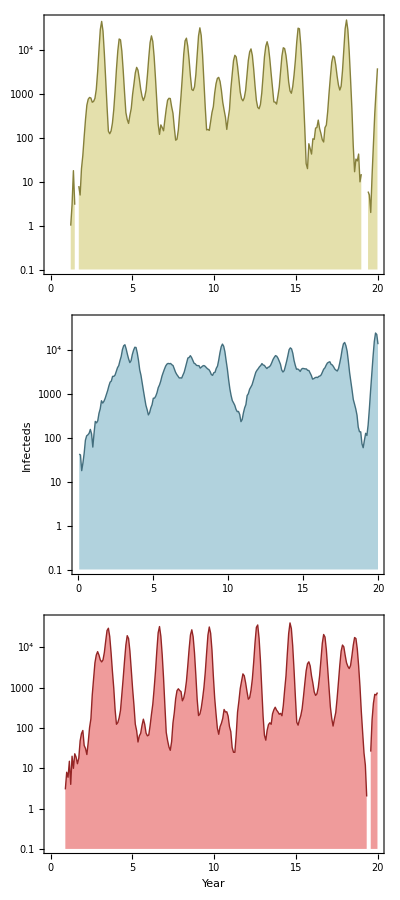

```mathematica
fig=Grid[Table[{ListLogPlot[prevList[[i]],PlotRange->{0.1,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Infecteds",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}},Joined->True]},{i,demeCount}]]
```

```mathematica
Export["prevalenceSpatialAbsolute.pdf",fig,"PDF"]
```

prevalenceSpatialAbsolute.pdf

### Deme-specific incidence

```mathematica
indices=Map[#<>"Cases"&,demes]/.headerRules
```

{17,25,33}

```mathematica
incList=N[Table[Transpose[{data[[All,date]],data[[All,i]]*100000/demePopSize}],{i,indices}]];
```

```mathematica
max=Max[Map[Max,incList[[All,All,2]]]]
```

13607.8

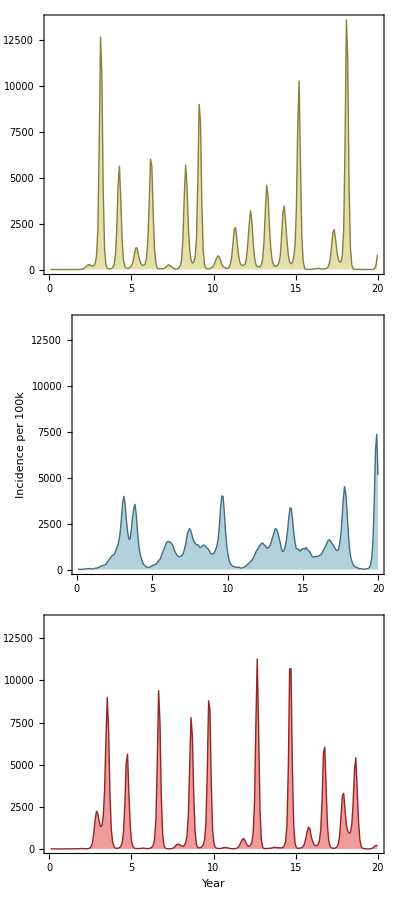

```mathematica
fig=Grid[Table[{ListLinePlot[incList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Incidence per 100k",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["incidenceSpatial.pdf",fig,"PDF"]
```

incidenceSpatial.pdf

### Diversity

```mathematica
index="div"/.headerRules
```

2

```mathematica
div=data[[All,{date,index}]];
```

```mathematica
meandiv=Mean[div][[2]]
```

2.76679

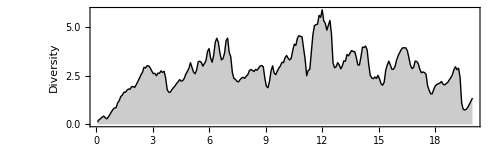

```mathematica
fig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"Year","Diversity"}]
```

```mathematica
Export["diversity.pdf",fig,"PDF"]
```

diversity.pdf

### Deme-specific diversity

```mathematica
indices=Map[#<>"Div"&,demes]/.headerRules
```

{10,18,26}

```mathematica
divList=N[Table[Transpose[{data[[All,date]],data[[All,i]]}],{i,indices}]];
```

```mathematica
meanDivList=Map[Mean[#]&,divList][[All,2]];
```

```mathematica
TableForm[Round[meanDivList,0.001],TableHeadings->{demes}]
```

north | 1.972
tropics | 2.486
south | 2.261

```mathematica
max=Max[Map[Max,divList[[All,All,2]]]]
```

6.4162

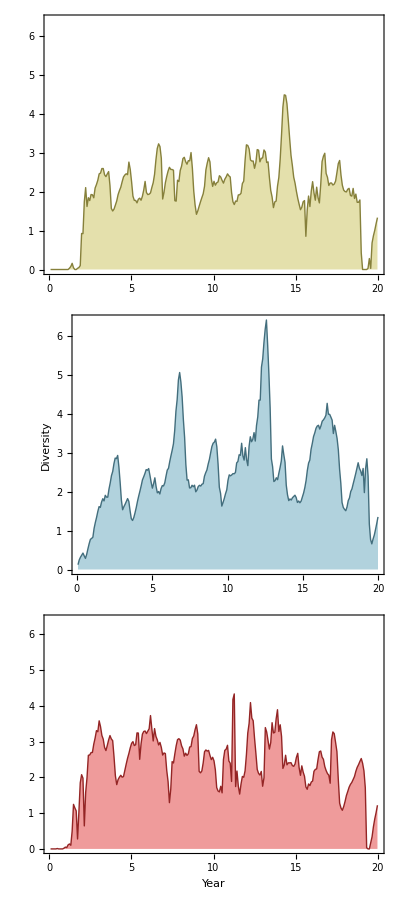

```mathematica
fig=Grid[Table[{ListLinePlot[divList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Diversity",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["diversitySpatial.pdf",fig,"PDF"]
```

diversitySpatial.pdf

### TMRCA

```mathematica
index="tmrca"/.headerRules
```

3

```mathematica
tmrca=data[[All,{date,index}]];
```

```mathematica
meantmrca=Mean[tmrca][[2]]
```

2.81285

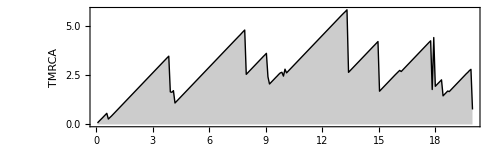

```mathematica
fig=ListLinePlot[tmrca,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"Year","TMRCA"}]
```

```mathematica
Export["tmrca.pdf",fig,"PDF"]
```

tmrca.pdf

### Deme-specific TMRCA

```mathematica
indices=Map[#<>"Tmrca"&,demes]/.headerRules
```

{11,19,27}

```mathematica
tmrcaList=N[Table[Transpose[{data[[All,date]],data[[All,i]]}],{i,indices}]];
```

```mathematica
meanTmrcaList=Map[Mean[#]&,tmrcaList][[All,2]];
```

```mathematica
TableForm[Round[meanTmrcaList,0.001],TableHeadings->{demes}]
```

north | 2.383
tropics | 2.668
south | 2.516

```mathematica
max=Max[Map[Max,tmrcaList[[All,All,2]]]]
```

5.789

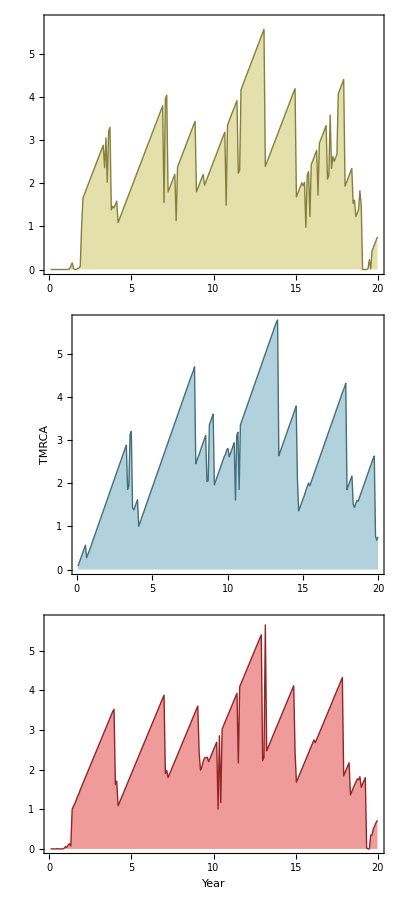

```mathematica
fig=Grid[Table[{ListLinePlot[tmrcaList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"TMRCA",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["tmrcaSpatial.pdf",fig,"PDF"]
```

tmrcaSpatial.pdf

### Ne*tau

```mathematica
index="netau"/.headerRules
```

4

```mathematica
netau=data[[All,{date,index}]];
```

```mathematica
netau=Select[netau,NumberQ[#[[2]]]&];
```

```mathematica
meannetau=Mean[netau][[2]]
```

74.4678

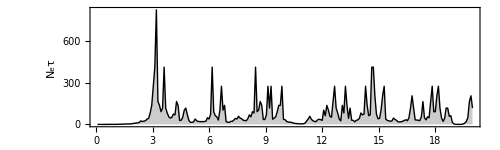

```mathematica
fig=ListPlot[netau,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"Year","N_eτ"},Joined->True]
```

```mathematica
Export["netau.pdf",fig,"PDF"]
```

netau.pdf

### Deme-specific Ne*tau

```mathematica
indices=Map[#<>"Netau"&,demes]/.headerRules
```

{12,20,28}

```mathematica
netauList=N[Table[Transpose[{data[[All,date]],data[[All,i]]}],{i,indices}]];
```

```mathematica
netauList=Map[Select[#,NumberQ[#[[2]]]&]&,netauList];
```

```mathematica
meanNetauList=Map[Mean[#]&,netauList][[All,2]];
```

```mathematica
TableForm[Round[meanNetauList,0.001],TableHeadings->{demes}]
```

north | 24.792
tropics | 23.875
south | 24.065

```mathematica
max=Max[Map[Max,netauList[[All,All,2]]]]
```

410.959

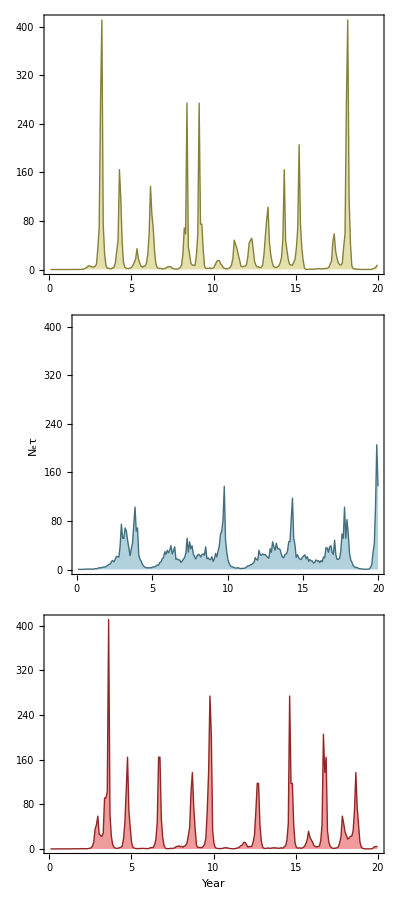

```mathematica
fig=Grid[Table[{ListLinePlot[netauList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"N_eτ",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["netauSpatial.pdf",fig,"PDF"]
```

netauSpatial.pdf

### Ne*tau vs prevalence

```mathematica
pairs=Select[Gather[Join[prevList[[1]],netauList[[1]]],#1[[1]]==#2[[1]]&],Length[#]==2&][[All,All,2]];
```

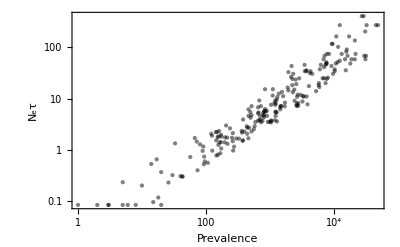

```mathematica
fig=ListLogLogPlot[pairs,PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->All,FrameLabel->{"Prevalence","N_eτ"},Frame->{True,True,False,False},Axes->False]
```

```mathematica
Export["prevVsNetau.pdf",fig,"PDF"]
```

prevVsNetau.pdf

## Virus samples

```mathematica
tipScale=0.0015;
```

```mathematica
tipData=Import["out.tips","CSV"];
```

```mathematica
traitHeader=tipData[[1]];
```

```mathematica
TableForm[traitHeader,TableHeadings->{Range[10]}]
```

1 | name
2 | year
3 | trunk
4 | tip
5 | mark
6 | location
7 | layout
8 | ag1
9 | ag2

```mathematica
tipData=Drop[tipData,1];
```

```mathematica
name=1;year=2;trunk=3;tip=4;mark=5;loc=6;layout=7;ag1=8;ag2=9;
```

### First tip

```mathematica
firstIndex=First[Ordering[tipData[[All,year]],1]]
```

2008

```mathematica
length=Length[tipData]
```

5963

### Graphics settings

```mathematica
frameWindow=1.0;
```

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-100,100,frameWindow}],{2},{2}];
```

### Map

```mathematica
noise[]:=With[{theta=RandomReal[{0,2Pi}],r=RandomVariate[ExponentialDistribution[1.9]]},
{r Cos[theta],r Sin[theta]}];
```

```mathematica
jitter=Map[#+noise[]&,tipData[[All,{ag1,ag2}]]];
```

```mathematica
plotRange={{Floor[Min[jitter[[All,1]]]],Ceiling[Max[jitter[[All,1]]]]},{Floor[Min[jitter[[All,2]]]],Ceiling[Max[jitter[[All,2]]]]}}
```

{{-3,59},{-6,3}}

```mathematica
avgDist[pointsA_,pointsB_]:=Mean[MapThread[EuclideanDistance,{RandomChoice[pointsA,1000],RandomChoice[pointsB,1000]}]]
```

```mathematica
clustered=FindClusters[jitter->Range[length],k,Method->{"Agglomerate","Linkage"->"Ward"},DistanceFunction->EuclideanDistance];
```

```mathematica
cluster[i_]:=jitter[[clustered[[i]]]]
```

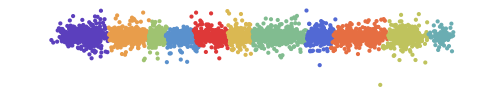

```mathematica
fig=ListPlot[Map[jitter[[#]]&,clustered],PlotStyle->clusterColors,AspectRatio->Automatic,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False]
```

```mathematica
Mean[Table[avgDist[cluster[i],cluster[i]],{i,k}]]
```

1.71434

```mathematica
Mean[Flatten[Table[Table[avgDist[cluster[i],cluster[j]],{j,i+1,k}],{i,k}]]]
```

21.2301

```mathematica
Export["mapClusters.pdf",fig,"PDF"]
```

mapClusters.pdf

### Cluster function

```mathematica
clusterCenters=Map[Mean[jitter[[#]]]&,clustered];
```

```mathematica
clusterFunction[p_]:=First[Nearest[clusterCenters->Range[k],p]]
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#]]],Point[#]}&,jitter];
```

```mathematica
Graphics[points,AspectRatio->Automatic,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95];
```

### AG1 vs AG2

```mathematica
tipScale=0.0025;
```

```mathematica
tallies=Tally[tipData[[All,{ag1,ag2}]]];
```

```mathematica
tallies=Sort[tallies,#1[[2]]>#2[[2]]&];
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#[[1]]]]],Disk[#[[1]],N[0.05*Sqrt[#[[2]]]]]}&,tallies];
```

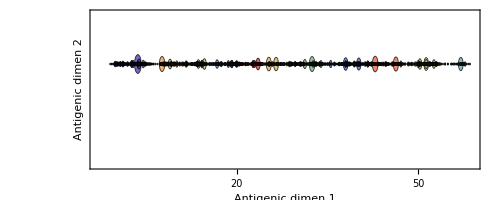

```mathematica
fig=Graphics[{EdgeForm[Thickness[0.0012]],Opacity[0.8],points},AspectRatio->Automatic,PlotRange->plotRange,FrameLabel->{"Antigenic dimen 1","Antigenic dimen 2"},Frame->{True,True,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-100,100,5}],None},{Table[{i,i,{0,0.005}},{i,-100,100,5}],None}},ImagePadding->fullPadding]
```

```mathematica
Export["virusAG1AG2.pdf",fig,"PDF"]
```

virusAG1AG2.pdf

### Distance from origin

```mathematica
dist[point_]:=EuclideanDistance[tipData[[firstIndex,{ag1,ag2}]],point]
```

```mathematica
list=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

```mathematica
meanFluxRate=(Max[list[[All,2]]]-Min[list[[All,2]]])/(Max[tipData[[All,year]]]-Min[tipData[[All,year]]])
```

2.99871

```mathematica
points=Map[{clusterColors[[clusterFunction[#[[{2,3}]]]]],PointSize[Small],Point[{#[[1]],dist[#[[{2,3}]]]}]}&,tipData[[All,{year,ag1,ag2}]]];
```

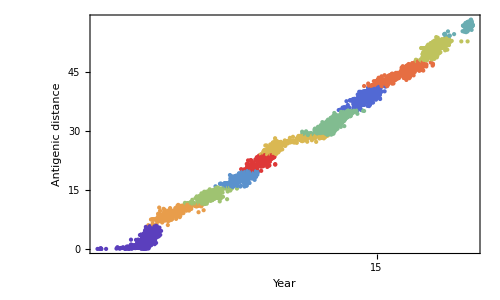

```mathematica
fig=Graphics[points,AspectRatio->0.6,FrameTicks->{{Table[{i,i,{0,0.005}},{i,0,100,5}],None},{Table[{i,i,{0,0.005}},{i,0,100,5}],None}},PlotRange->All,FrameLabel->{"Year","Antigenic distance"},Frame->{True,True,False,False},ImagePadding->fullPadding]
```

```mathematica
Export["virusYearDistance.pdf",fig,"PDF"]
```

virusYearDistance.pdf

### Cluster turnover

```mathematica
times=tipData[[All,year]];
```

```mathematica
step=N[(4*7)/365];
```

```mathematica
step=stepTime;
```

```mathematica
clusters=Map[times[[#]]&,clustered];
```

```mathematica
datelist=Table[i,{i,step,endTime,step}];
```

```mathematica
totalCounts=BinCounts[Flatten[clusters],{0,endTime,step}];
```

```mathematica
pro=Table[DeleteCases[N[MapThread[If[#2==0,Null,{#3,#1/#2}]&,{BinCounts[clusters[[i]],{0,endTime,step}],totalCounts,datelist}]],Null],{i,k}];
```

```mathematica
loess=Table[Map[{#,LoessFit[#,pro[[j]],0.05,1]}&,Table[i,{i,incList[[1,All,1]]}]],{j,k}];
```

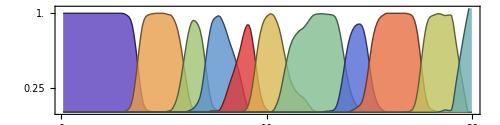

```mathematica
Show[Table[ListLinePlot[loess[[j]],Filling->Axis,FillingStyle->Directive[Opacity[0.8],clusterColors[[j]]],PlotStyle->Directive[Darker[clusterColors[[j]],0.5]],AspectRatio->0.25,PlotRange->{0,1.05},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-0.5,1,0.25}],None},{Table[{i,i,{0,0.005}},{i,0,40,10}],None}}],{j,k}]]
```

### Prevelance sorted by cluster

```mathematica
minFrequency=0.1;
```

```mathematica
clusterEmergences[i_]:=With[{dates=loess[[i,All,1]][[Flatten[Position[loess[[i,All,2]],x_/;x>minFrequency]]]]},{Min[dates],Max[dates]}]
```

```mathematica
clusterDuration[i_]:=With[{dates=loess[[i,All,1]][[Flatten[Position[loess[[i,All,2]],x_/;x>minFrequency]]]]},Max[dates]-Min[dates]]
```

```mathematica
durations=Table[clusterDuration[i],{i,k}]
```

{3.863,2.7945,1.6439,2.3014,1.8904,2.7123,3.6987,1.8082,3.1233,2.3835,0.8219}

```mathematica
transitionTimes=MapThread[#1[[2]]-#2[[1]]&,{Table[clusterEmergences[i],{i,1,k-1}],Table[clusterEmergences[i],{i,2,k}]}]
```

{0.4931,0.6576,0.5754,1.0685,0.5753,1.3973,0.7397,0.6576,0.4931,0.4931}

```mathematica
maxInc=Max[Flatten[Table[MapThread[#1[[2]]*#2[[2]]&,{incList[[i]],loess[[j]]}],{i,demeCount},{j,k}]]]
```

13308.9

```mathematica
incFig[deme_]:=Show[Table[ListLinePlot[MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{incList[[deme]],loess[[j]]}],Filling->Axis,FillingStyle->Directive[Opacity[0.8],clusterColors[[j]]],PlotStyle->Directive[Darker[clusterColors[[j]],0.5]],AspectRatio->0.25,PlotRange->{0,maxInc},FrameTicks->{{Table[{i,i,{0,0.005}},{i,0,20000,5000}],None},{Table[{i,i,{0,0.005}},{i,0,40,5}],None}},FrameLabel->{If[deme==demeCount,"Year",""],If[deme==2,"Incidence per 100k",""]},ImagePadding->{{50,10},{If[deme==demeCount,30,15],5}}],{j,k}]]
```

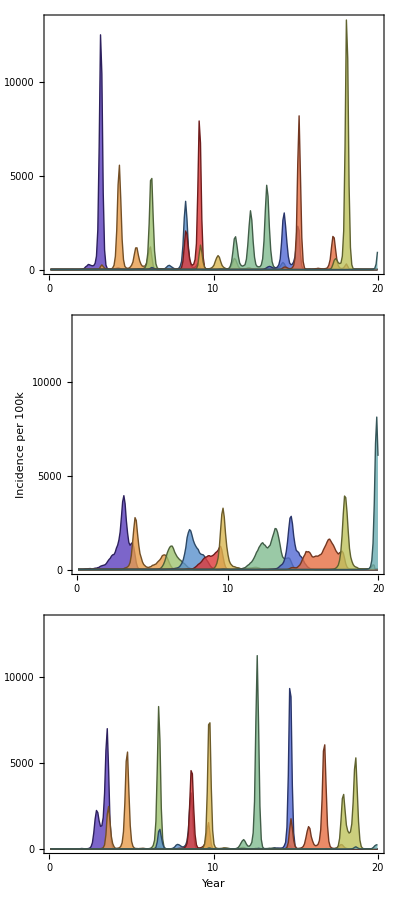

```mathematica
fig=Grid[Table[{incFig[i]},{i,demeCount}]]
```

```mathematica
Export["incidenceClustersSpatial.pdf",fig,"PDF"]
```

incidenceClustersSpatial.pdf

```mathematica
totals=Accumulate[Join[{Table[0,{Length[Table[i,{i,incList[[1,All,1]]}]]}]},Reverse[loess[[All,All,2]]]]];
```

```mathematica
totals=MapIndexed[{#2[[2]]*stepTime,#1}&,totals,{2}];
```

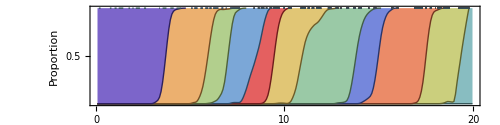

```mathematica
fig=ListLinePlot[totals,Filling ->Table[i->{{i+1},Directive[Opacity[0.8],clusterColors[[k+1-i]]]},{i,k}],PlotStyle->Table[Directive[Darker[clusterColors[[k+1-i]],0.5]],{i,k}],AspectRatio->0.25,FrameTicks->{{Table[{i,i,{0,0.005}},{i,-0.5,1,0.5}],None},{Table[{i,i,{0,0.005}},{i,0,40,5}],None}},PlotRange->{0,1},FrameLabel->{"Year","Proportion"},ImagePadding->fullPadding]
```

```mathematica
Export["clusterTurnover.pdf",fig,"PDF"]
```

clusterTurnover.pdf

## Spatial / antigenic comparison

### Loess spline

```mathematica
data=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

```mathematica
fit[x_]:=LoessFit[x,data,0.2,1]
```

```mathematica
startTime=Min[data[[All,1]]]
```

0.5014

```mathematica
endTime=Max[data[[All,1]]]
```

19.9863

```mathematica
max=Max[data[[All,2]]]
```

58.4295

```mathematica
loessList=Table[{x,fit[x]},{x,startTime,endTime,0.1}];
```

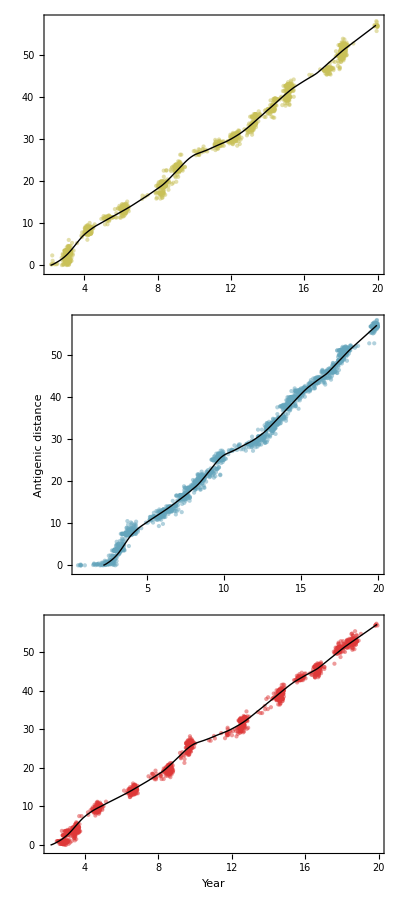

```mathematica
fig=Grid[Table[{Show[ListPlot[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]],PlotStyle->Directive[i/.spatialColorRules,Opacity[0.5]],PlotRange->{-1,max},ImagePadding->{{30,5},{If[i==2,35,10],5}},AspectRatio->0.5,FrameLabel->{If[i==2,"Year",""],If[i==1,"Antigenic distance",""]},ImageSize->400],ListLinePlot[loessList,PlotStyle->Directive[Black,Thick]]]},{i,0,demeCount-1}]]
```

```mathematica
Export["virusYearDistanceSpatial.pdf",fig,"PDF"]
```

virusYearDistanceSpatial.pdf

```mathematica
distance[list_]:=Module[{nf},
nf=Nearest[loessList[[All,1]]->loessList[[All,2]]];
Map[#[[2]]-First[nf[#[[1]]]]&,list]
]
```

```mathematica
Mean[distance[data]]
```

-0.0131827

```mathematica
standardError[list_]:=StandardDeviation[list]/Sqrt[Length[list]]
```

```mathematica
standardError[distance[data]]
```

0.013356

```mathematica
spatialDists=Table[With[{dist=distance[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]]]},{Mean[dist]-standardError[dist],Mean[dist],Mean[dist]+standardError[dist]}],{i,0,demeCount-1}];
```

```mathematica
{meanDistNorth,meanDistTropics,meanDistSouth}=Table[With[{dist=distance[Map[{#[[1]],dist[#[[{2,3}]]]}&,Select[tipData,(#[[loc]]==i)&][[All,{year,ag1,ag2}]]]]},Mean[dist]],{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[spatialDists,0.001],TableHeadings->{demes,{"95% lower","mean","95% upper"}}]
```

| 95% lower | mean | 95% upper
north | -0.049 | -0.026 | -0.003
tropics | 0.207 | 0.231 | 0.255
south | -0.264 | -0.243 | -0.222

```mathematica
chart=MapIndexed[{GrayLevel[0.3],Line[{{#1[[1]],demeCount-#2[[1]]},{#1[[3]],demeCount-#2[[1]]}}],Line[{{#1[[1]],demeCount-#2[[1]]+0.1},{#1[[1]],demeCount-#2[[1]]-0.1}}],Line[{{#1[[3]],demeCount-#2[[1]]+0.1},{#1[[3]],demeCount-#2[[1]]-0.1}}],PointSize[0.03],spatialColors[[#2[[1]]]],Point[{#1[[2]],demeCount-#2[[1]]}]}&,spatialDists];
```

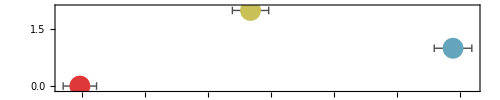

```mathematica
fig=Graphics[chart,AspectRatio->0.2,PlotRange->All,Frame->{True,False,True,False},PlotRangePadding->{{0,0},{0.5,0.5}},FrameLabel->{"Distance to AG spline"}]
```

```mathematica
Export["lagAG1Spatial.pdf",fig,"PDF"]
```

lagAG1Spatial.pdf

## Tree

### Data import

First node is child, second is parent

```mathematica
branchScale=0.001;tipScale=0.0015;clip=0.005;
```

```mathematica
getThickness[count_]:=Thickness[Clip[branchScale*N[Sqrt[count]],{0,clip}]]
```

```mathematica
getPointSize[count_]:=PointSize[N[tipScale*Sqrt[count]]];
```

```mathematica
name=1;year=2;trunk=3;tip=4;mark=5;loc=6;layout=7;ag1=8;ag2=9;
```

```mathematica
branchData=ToExpression[Import["out.branches","Table"]];
```

```mathematica
branchData[[1]]
```

{{740b4818,0.2384,1,0,1,1,41.6473,0.,0.},{7d2f117,0.,1,0,1,0,41.6473,0.,0.},5963}

```mathematica
branchData[[1,{1,2},{year,layout}]]
```

{{0.2384,41.6473},{0.,41.6473}}

### Reduction

Using a subset of the viruses for tree visualization

```mathematica
slimBranches=Select[branchData,(#[[1,mark]]==1&&#[[2,mark]]==1&)];
```

```mathematica
Length[Select[slimBranches,(#[[1,tip]]==1&)]]
```

182

### Time vs Layout with clusters

```mathematica
branchLines=Map[{Thickness[0.0025],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

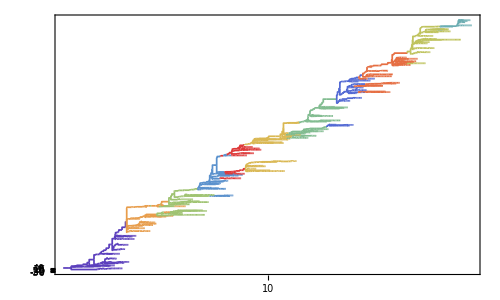

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,FrameLabel->{"Year"},Frame->{True,False,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,5}],None},{Table[{i,i,{0,0.005}},{i,-50,50,5}],None}},ImagePadding->partialPadding]
```

```mathematica
Export["treeClusters.pdf",fig,"PDF"]
```

treeClusters.pdf

### Time vs Layout with location

```mathematica
branchLines=Map[{Thickness[0.0025],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

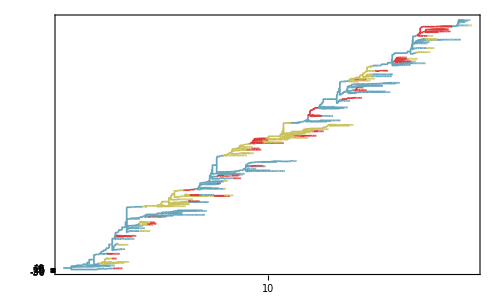

```mathematica
fig=Graphics[branchLines,AspectRatio->0.6,PlotRange->All,FrameLabel->{"Year"},Frame->{True,False,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,5}],None},{Table[{i,i,{0,0.005}},{i,-50,50,5}],None}},ImagePadding->partialPadding]
```

```mathematica
Export["treeSpatial.pdf",fig,"PDF"]
```

treeSpatial.pdf

### Time vs AG1 with clusters

```mathematica
branchLines=Map[{Thickness[0.0025],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{year,ag1}]],#[[2,{year,ag1}]]}]}&,slimBranches];
```

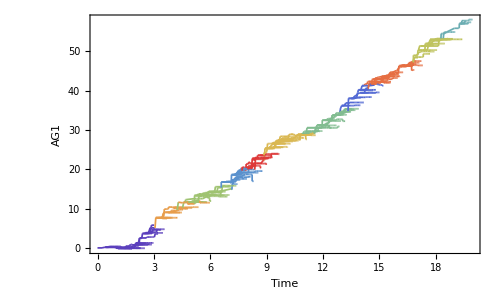

```mathematica
fig=Graphics[{CapForm["Round"],branchLines},AspectRatio->0.6,PlotRange->All,FrameLabel->{"Time","AG1"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeYearAG1Clusters.pdf",fig,"PDF"]
```

treeYearAG1Clusters.pdf

### AG1 vs AG2 with clusters

```mathematica
mutBranches=Select[slimBranches,(EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001&)];
```

```mathematica
branchLines=Map[{Thickness[0.0025],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}],clusterColors[[clusterFunction[#[[2,{ag1,ag2}]]]]],Line[{Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}],#[[2,{ag1,ag2}]]}]}&,mutBranches];
```

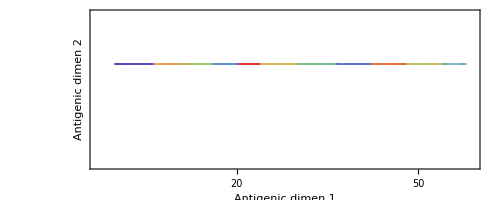

```mathematica
agtree=Graphics[{CapForm["Round"],branchLines},AspectRatio->Automatic,PlotRange->plotRange,Frame->{True,True,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-100,100,5}],None},{Table[{i,i,{0,0.005}},{i,-100,100,5}],None}},FrameLabel->{"Antigenic dimen 1","Antigenic dimen 2"}]
```

```mathematica
Export["treeAG1AG2Clusters.pdf",agtree,"PDF"]
```

treeAG1AG2Clusters.pdf

## Migration statistics

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&&#[[1,year]]<endTime-5&)];
```

```mathematica
sideBranches=Select[branchData,(#[[1,trunk]]==0&&#[[1,year]]<endTime-5&)];
```

### Proportion of each deme in trunk

```mathematica
trunkLengths=Table[Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,Select[trunkBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)]]],{i,0,demeCount-1}];
```

```mathematica
trunkProportions=trunkLengths/Total[trunkLengths];
```

```mathematica
{trunkProNorth,trunkProTropics,trunkProSouth}=trunkLengths/Total[trunkLengths];
```

```mathematica
TableForm[Round[trunkProportions,0.001],TableHeadings->{demes}]
```

north | 0.388
tropics | 0.503
south | 0.11

### Migration rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[#[[1,loc]]≠#[[2,loc]],1,0]&,sideBranches]];
```

```mathematica
trunkMigRate=trunkCount/trunkOpportunity
```

0.736831

```mathematica
sideBranchMigRate=sideBranchCount/sideBranchOpportunity
```

0.19987

### Migration matrix -- trunk

```mathematica
trunkCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,trunkBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
trunkRates=(trunkCounts/trunkOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[Round[trunkRates,0.001]/.(0.->""),TableHeadings->{demes,demes}]
```

| north | tropics | south
north |  | 0.369 | 0.369
tropics | 0.427 |  | 0.142
south | 0.653 | 1.306 |

### Migration matrix -- side branches

```mathematica
sideBranchCounts=Table[Total[Map[If[#[[1,loc]]==j&&#[[2,loc]]==i,1,0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchOpportunies=Table[Total[Map[If[#[[1,loc]]==i&&#[[2,loc]]==i,Abs[#[[1,year]]-#[[2,year]]],0]&,sideBranches]],{i,0,demeCount-1},{j,0,demeCount-1}];
```

```mathematica
sideBranchRates=(sideBranchCounts/sideBranchOpportunies)*(1-DiagonalMatrix[Table[1,{demeCount}]]);
```

```mathematica
TableForm[Round[sideBranchRates,0.001]/.(0.->""),TableHeadings->{demes,demes}]
```

| north | tropics | south
north |  | 0.055 | 0.194
tropics | 0.109 |  | 0.115
south | 0.064 | 0.054 |

## Antigenic statistics

```mathematica
trunkBranches=Select[branchData,(#[[1,trunk]]==1&&#[[1,year]]<endTime-5&)];
```

```mathematica
sideBranches=Select[branchData,(#[[1,trunk]]==0&&#[[1,year]]<endTime-5&)];
```

### Mutation rate

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,trunkBranches]];
```

```mathematica
sideBranchCount=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,sideBranches]];
```

```mathematica
trunkMutationRate=trunkCount/trunkOpportunity
```

3.81812

```mathematica
sideBranchMutationRate=sideBranchCount/sideBranchOpportunity
```

1.91155

### Antigenic flux

```mathematica
trunkOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,trunkBranches]];
```

```mathematica
sideBranchOpportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,sideBranches]];
```

```mathematica
trunkDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches]];
```

```mathematica
sideBranchDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches]];
```

```mathematica
trunkFluxRate=trunkDistance/trunkOpportunity
```

3.13154

```mathematica
sideBranchFluxRate=sideBranchDistance/sideBranchOpportunity
```

0.637488

### Mutation size

```mathematica
trunkMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,trunkBranches],#>0.0000001&];
```

```mathematica
sideBranchMutations=Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,sideBranches],#>0.0000001&];
```

```mathematica
trunkMutationSize=Mean[trunkMutations]
```

0.820179

```mathematica
sideBranchMutationSize=Mean[sideBranchMutations]
```

0.333493

### Combined

```mathematica
TableForm[Round[{{sideBranchMutationRate,sideBranchMutationSize,sideBranchFluxRate},{trunkMutationRate,trunkMutationSize,trunkFluxRate}},0.001],TableHeadings->{{"Side branches","Trunk branches"},{"Mutation rate","Mutation size","Antigenic flux"}}]
```

| Mutation rate | Mutation size | Antigenic flux
Side branches | 1.912 | 0.333 | 0.637
Trunk branches | 3.818 | 0.82 | 3.132

### Mutation rate - spatial

```mathematica
trunkRates=Table[
branches=Select[trunkBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
count=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,branches]];
rate=count/opportunity,
{i,0,demeCount-1}];
```

```mathematica
sideBranchRates=Table[
branches=Select[sideBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
count=Total[Map[If[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001,1,0]&,branches]];
rate=count/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[{sideBranchRates,trunkRates},0.001],TableHeadings->{{"Side branches","Trunk branches"},demes}]
```

| north | tropics | south
Side branches | 1.984 | 1.897 | 1.899
Trunk branches | 4.977 | 3.841 | 1.959

### Mutation size - spatial

```mathematica
trunkSize=Table[
branches=Select[trunkBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
Mean[Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches],#>0.0000001&]],
{i,0,demeCount-1}];
```

```mathematica
sideBranchSize=Table[
branches=Select[sideBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
Mean[Select[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches],#>0.0000001&]],
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[{sideBranchSize,trunkSize},0.001],TableHeadings->{{"Side branches","Trunk branches"},demes}]
```

| north | tropics | south
Side branches | 0.317 | 0.349 | 0.33
Trunk branches | 0.673 | 0.924 | 1.215

### Antigenic flux - spatial

```mathematica
trunkRates=Table[
branches=Select[trunkBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
rate=antigenicDistance/opportunity,
{i,0,demeCount-1}];
```

```mathematica
sideBranchRates=Table[
branches=Select[sideBranches,(#[[1,loc]]==i&&#[[2,loc]]==i&)];
opportunity=Total[Map[Abs[#[[1,year]]-#[[2,year]]]&,branches]];
antigenicDistance=Total[Map[EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]&,branches]];
rate=antigenicDistance/opportunity,
{i,0,demeCount-1}];
```

```mathematica
TableForm[Round[{sideBranchRates,trunkRates},0.001],TableHeadings->{{"Side branches","Trunk branches"},demes}]
```

| north | tropics | south
Side branches | 0.629 | 0.663 | 0.627
Trunk branches | 3.347 | 3.549 | 2.38